# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Utility Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Needs

```mathematica
Needs["Steiner`Utilities`", "packages\\steiner_utilities.wl"]
```

```mathematica
Needs["LeftistHeap`", "packages\\data_structures\\leftist_heap.wl"]
```

```mathematica
Needs["Steiner`Algorithms`GraphUtilities`", "packages\\steiner_algorithms_graph_utilities.wl"]
```

```mathematica
Needs["Steiner`Generator`", "packages\\steiner_generator.wl"]
Needs["Steiner`SteinLib`", "packages\\steiner_steinlib.wl"]
```

```mathematica
Needs["Steiner`Visualization`", "packages\\steiner_visualization.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Exact`", "packages\\steiner_algorithms_exact.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Voronoi`", "packages\\steiner_algorithms_voronoi.wl"]
Needs["Steiner`Algorithms`Approximation`", "packages\\steiner_algorithms_approximation.wl"]
```

```mathematica
Needs["TestingSystem`", "packages\\testing_system.wl"]
```

## Input data

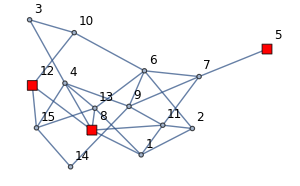

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstance[15, 3, BernoulliProbability->0.25];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12]]
```

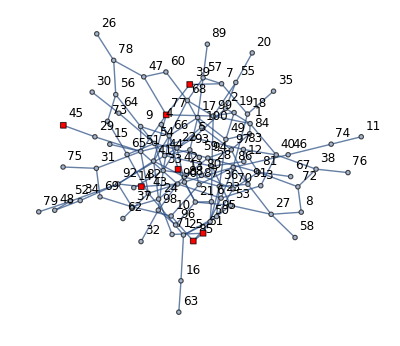

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstance[100, 7, BernoulliProbability->0.028];
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,12], TerminalSize->1.25, ImageSize->400]
```

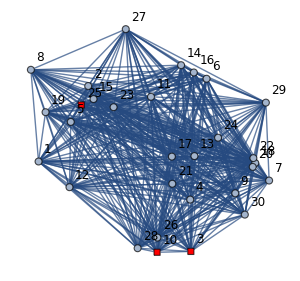

```mathematica
{graph2D, weightAssociation2D, terminals2D} = generate2DSteinerProblemInstance[30, 3];
drawGraph[graph2D, terminals2D, VertexLabelStyle->Directive[Black,12], VertexSize->1.5]
```

```mathematica
getInstancesList["\\steinlib\\D"]
```

{E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d01.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d02.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d03.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d04.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d05.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d06.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d07.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d08.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d09.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d10.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d11.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d12.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d13.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d14.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d15.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d16.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d17.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d18.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d19.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d20.stp}

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["\\steinlib\\D\\d15.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

1000

5000

500

## Visualization

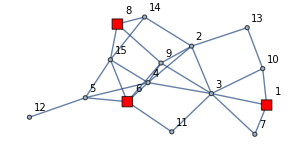

```mathematica
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,10]]
```

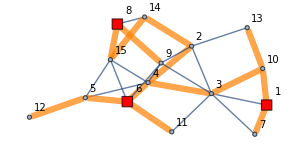

```mathematica
drawGraphSubgraph[graph15, FindSpanningTree[graph15]//EdgeList, terminals15, VertexLabelStyle->Directive[Black,10]]
```

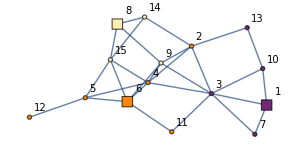

```mathematica
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10], VertexStyleFunc->voronoiVertexStyle[VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]]]]
```

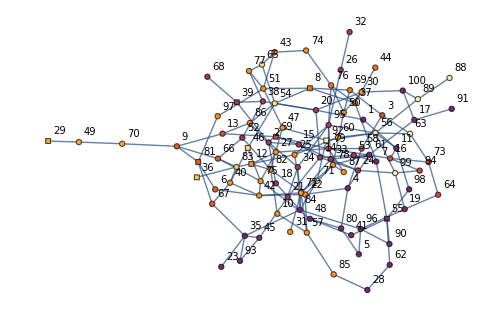

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10], VertexStyleFunc->voronoiVertexStyle[VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals100]["voronoi"]]],
TerminalSize->1.25, ImageSize->500]
```

```mathematica
dijkstraVoronoi[graph15, terminals15];
voronoiVertexStyle[VertexList@graph15, Normal[%["voronoi"]]]⟦%["order"]⟧;
Manipulate[
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
 VertexStyleFunc->%⟦;;step⟧]
,
{step, 1, 15, 1}]
```

```mathematica
dijkstraVoronoi[graph100, terminals100];
voronoiVertexStyle[VertexList@graph100, Normal[%["voronoi"]]]⟦%["order"]⟧;
Manipulate[
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10], VertexStyleFunc->(%⟦;;step⟧),
TerminalSize->2.5, ImageSize->500],
{step, 1, 100, 1}]
```

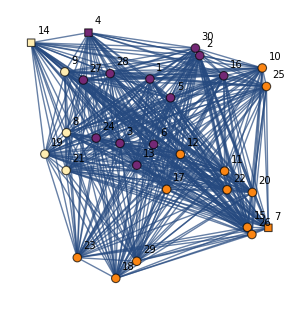

```mathematica
drawGraph[graph2D,terminals2D, VertexLabelStyle->Directive[Black,10], VertexStyleFunc->voronoiVertexStyle[VertexList@graph2D, Normal[dijkstraVoronoi[graph2D, terminals2D]["voronoi"]]], VertexSize->1]
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description

```mathematica
-Graphics-
-Graphics-
```

Asymptotic time is : O (3^t n+2^t n^2), where t = #Terminals. n = #Vertices.

#### 15

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
resultDreyfusWagner15
```

{0.0127081,Null}

150.

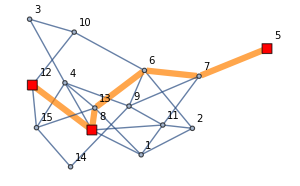
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 150.

```mathematica
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

#### 100 Verts

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
resultDreyfusWagner100
```

{13.8596,Null}

835.

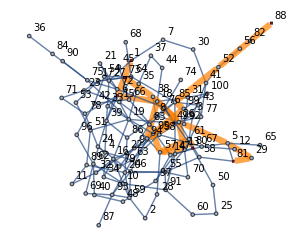
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 790.

```mathematica
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

#### Stlib

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultDreyfusWagnerStlibTest
```

{0.0491777,Null}

7.

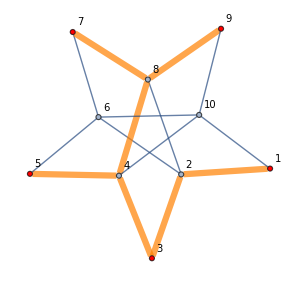
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7.

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagnerStlibTest, stlibTestWeights]
```

7

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### 2-approximation (Mehlhorn) [8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi separation of graph.
	- new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Refind original short-path graph accorgind to spanning tree.
4. Find MinSpanningTree in it.
5. Cut it, to make Steiner-tree.

### Examples

#### 15 Verts

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0030847,Null}

150

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 150

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[treeMehlhorn15, weightAssociation15]
```

{0.0058757,Null}

150

```mathematica
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 150

#### 100 Verts

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{0.0619477,Null}

912

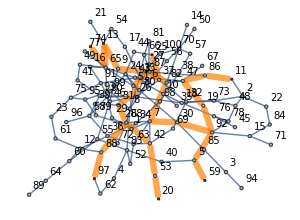
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 912

```mathematica
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{0.0117251,Null}

898

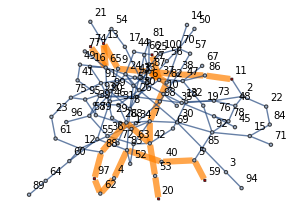
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 898

```mathematica
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

#### Stlib

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[treeMehlhornStlibTest, stlibTestWeights]
```

{1.51774,Null}

1137

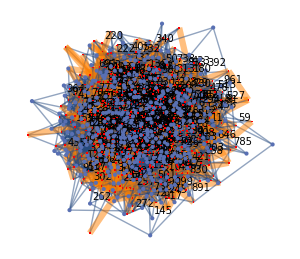
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1137

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest]
```

## Greedy algorithms [6][7]

### SPH

### multiple SPH

## Data Structures

### Leftist heap

```mathematica
n=10000;
tmp = RandomInteger[{1, 1000}, {n, 2}];
(t1 = leftistHeapHeapify[tmp]);//AbsoluteTiming
(Do[leftistExtractMin[t1], n]);//AbsoluteTiming
```

{0.190427,Null}

{0.926045,Null}

```mathematica
ds = CreateDataStructure["PriorityQueue"];
n=10000;
tmp = RandomInteger[{1, 1000}, {n, 2}];
(ds["Push", #]&/@tmp);//AbsoluteTiming
Do[ds["Pop"], n]//AbsoluteTiming
```

{0.0158709,Null}

{0.0323065,Null}

```mathematica
n= 10000;
tmp1 = RandomInteger[{1, 1000}, {n, 2}];
(h1 = leftistHeapHeapify[tmp1]);//AbsoluteTiming
tmp2 = RandomInteger[{1, 1000}, {n, 2}];
(h2 = leftistHeapHeapify[tmp2]);//AbsoluteTiming
(h3 = leftistHeapMeld[h1, h2]);//AbsoluteTiming
```

{0.192941,Null}

{0.203171,Null}

{0.0000942,Null}

```mathematica
n=10000;
ds1 = CreateDataStructure["PriorityQueue"];
tmp1 = RandomInteger[{1, 1000}, {n, 2}];
(ds1["Push", #]&/@tmp1);//AbsoluteTiming
ds2 = CreateDataStructure["PriorityQueue"];
tmp2 = RandomInteger[{1, 1000}, {n, 2}];
(ds2["Push", #]&/@tmp2);//AbsoluteTiming
Do[ds1["Push", ds2["Pop"]], n];//AbsoluteTiming
```

{0.0150612,Null}

{0.013447,Null}

{0.0370936,Null}

### Dynamic forest

## Local-search algorithms [7]

### Steiner-Vertex Insertion

### Steiner-Vertex Elimination

### Key-Path Exchange

### Key-Vertex Elimination

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - nice paper

## ToDo List

```mathematica
"
- Исправить восстановление дерева в DW
- Эвристики для больших графов.
-- Жадные (old)
-- Локальный поиск (2010)
- Провести тесты
"

"
? - Точная постановка.
? - Алгоритм с 1.53 приближением.
? - Prunning and predprocessing.
? - Ускоренный на separation's DW (2007)
"

"
Done:
- Melhorn
- Дописать в тестер возможность модельных данных
- Протестировать на модельных (библиотечных) данных.
"
```

```mathematica
circuit design,networking,and computational biology
```